```mathematica
(*ClearAll["Global`*"]*)

(*aux: type punning*)
signedToUnsigned[x_, b_:32]:=Module[{val=x, bits=b},
If[Negative[val],
nd=IntegerDigits[val,2];                                                  (* truncate extra digits *)
If[Length[nd]>bits,val=FromDigits[Take[nd,-bits],2],val];
val=Abs[val];                                                                            (* 1's complement *)
n=BitXor[val,FromDigits[ ConstantArray[1,bits],2]];
n+=1,                                                                                             (* 2's complement *)
(* else, nothing to do, just truncate it to spec bits *)
nd=IntegerDigits[val,2];                                                  (* truncate extra digits *)
If[Length[nd]>bits,val=FromDigits[Take[nd,-bits],2],val];
val]
];
realToInt32[x_]:=Module[{xx=x},
realbits=IntegerDigits[xx,2];
If[Length[realbits]>32,
int32bits=Take[realbits,-32];  (* take last 32 slots, aka first for 32bits *)
int32=FromDigits[int32bits,2];
int32, (*else*)
xx]
];

(*convert samples from 0-1 to -1-+1*)
convertSample[kx_]=2.0*kx-1.0;
```

```mathematica
(* -- Halton Sampler -- *)
haltonSample[kb_Integer,kj_Integer]:=Module[{b=kb,j=kj},

primes={2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71};
(*primes={1,9,19,13,6,2,8,3,10,7,12,4,5,14,18,16,15,17,20,11};*)
rev[ki_Integer,kp_Integer]:=If[ki==0,ki,kp-ki];

p=primes[[b+1]]; (*1-base array*)
h=0.0;
f=1.0/p;
fct=f;
While[j>0,
h+=rev[Mod[j,p],p]*fct;
j=IntegerPart[j/p];
fct*=f;
];
h
]
(*this is freaking slow here on Mathematica*)
(*but it's way faster(3x) on C++ than above based on perms*)
(*and together with haltonSample3 has a better quality*)
haltonSample2[kidx_Integer]:=Module[{idx=signedToUnsigned[kidx]},
idx=BitOr[BitShiftLeft[idx,16],BitShiftRight[idx,16]];
idx=BitOr[BitShiftLeft[BitAnd[idx,Interpreter["HexInteger"]["00ff00ff"]],8],BitShiftRight[BitAnd[idx,Interpreter["HexInteger"]["ff00ff00"]],8]];
idx=BitOr[BitShiftLeft[BitAnd[idx,Interpreter["HexInteger"]["0f0f0f0f"]],4],BitShiftRight[BitAnd[idx,Interpreter["HexInteger"]["f0f0f0f0"]],4]];
idx=BitOr[BitShiftLeft[BitAnd[idx,Interpreter["HexInteger"]["33333333"]],2],BitShiftRight[BitAnd[idx,Interpreter["HexInteger"]["cccccccc"]],2]];
idx=BitOr[BitShiftLeft[BitAnd[idx,Interpreter["HexInteger"]["55555555"]],1],BitShiftRight[BitAnd[idx,Interpreter["HexInteger"]["aaaaaaaa"]],1]];
idx*1.0/BitShiftLeft[1,32]
]
haltonSample3[kidx_Integer]:=Module[{idx=signedToUnsigned[kidx]},
result=0.0;
scale=1.0;
While[idx≠0,
scale/=3.0;
result+=Mod[idx,3]*scale;
idx=IntegerPart[idx/3];
];
result
]

wangHash[kx_Integer]:=Module[{x=signedToUnsigned[kx]},
x=BitXor[BitXor[x,61],BitShiftRight[x,16]];
x*=9;
x=BitXor[x,BitShiftRight[x,4]];
x=signedToUnsigned[x*Interpreter["HexInteger"]["27d4eb2d"]];
x=BitXor[x,BitShiftRight[x,15]];
x
]
lowBias32Hash[kx_Integer]:=Module[{x=signedToUnsigned[kx]},
x=BitXor[x,BitShiftRight[x,16]];
x=signedToUnsigned[x*Interpreter["HexInteger"]["7feb352d"]];
x=BitXor[x,BitShiftRight[x,15]];
x=signedToUnsigned[x*Interpreter["HexInteger"]["846ca68b"]];
x=BitXor[x,BitShiftRight[x,16]];
x
]
iqHash[kx_Integer,ky_Integer:0]:=Module[{x=signedToUnsigned[kx],
                                                                                     y=signedToUnsigned[ky]},
qx=signedToUnsigned[r2C0*BitXor[BitShiftRight[x,r2C1],x]];
qy=signedToUnsigned[r2C0*BitXor[BitShiftRight[y,r2C1],y]];
n=signedToUnsigned[r2C0*BitXor[qx,BitShiftRight[qy,r2C3]]];
hsh=n*(1.0/r2C2);
hsh
]

haltonSampler1D[kidx_Integer]:=Module[{idx=kidx},
idx=wangHash[idx];
haltonSample3[idx]
]
haltonSampler2D[kidx_Integer]:=Module[{idx=kidx},
s1=haltonSample[1,idx];
s2=haltonSample[2,idx];
{s1,s2}
]
haltonSampler2DX[kidx_Integer]:=Module[{idx=kidx},
s1=haltonSample2[idx];
s2=haltonSample3[idx];
{s1,s2}
]
haltonSampler2DLB[kidx_Integer]:=Module[{idx=kidx},
idx=lowBias32Hash[idx];
s1=haltonSample2[idx];
s2=haltonSample3[idx];
{s1,s2}
]
haltonSampler3D[kidx_Integer]:=Module[{idx=kidx},
s1=haltonSample[1,idx];
s2=haltonSample[2,idx];
s3=haltonSample[3,idx];
{s1,s2,s3}
]
```

```mathematica
haltonSampler1D[1234578]
```

0.687581

```mathematica
(*
Manipulate[Module[{data,inside,insidepts},SeedRandom[n];
(*data=RandomReal[{-1,1},{m,2}];*)
p=hashInt2D[10,10];
rdata=ParallelTable[ haltonSampler2D[i],{i,m}];
data=Map[convertSample,rdata];
insidepts=Cases[data,{x_,y_}/;x^2+y^2<1];
inside=Length[insidepts];·
Text@Style[
Column[{Graphics[{PointSize[0.006],RGBColor[0.17,0.5,0.75],Disk[{0,0},1],Black,Point[data]},ImageSize->If[format,500,350]],Row[{"inside: ",inside,"\toutside: ",m-inside,"\ttotal:  ",m}],Row[{"π ≈ 4 × ",inside,"/",m," = ",4. inside/m}]}],"Label"]],{{n,1,"random seed"},1,1000,1},{{m,1,"sample size"},64,8192,64,Appearance->"Labeled"},{{format,False,"large format"},{True,False}},AutorunSequencing->{1,2}]
*)
```

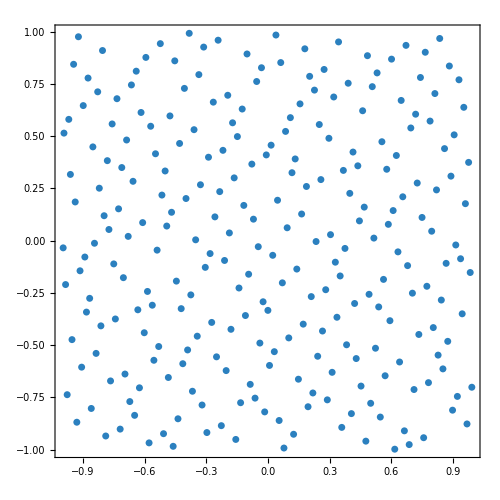

```mathematica
(*
rdata=ParallelTable[ With[{i=i},haltonSampler2DX[i]],{i,256}];
data=Map[convertSample,rdata];

Graphics[
{
PointSize[0.01],
RGBColor[0.17,0.5,0.75],
Point[data]
},
ImageSize->If[True,500,350],
Frame->True]
*)
```

See .. Cache-Friendly Micro-Jittered Sampling paper .. to micro-jitter Halton seqs